# Mutation recurrence distribution plots

## Data import

```mathematica
path = ".";
```

```mathematica
project = "all"
```

all

```mathematica
chompedFiles = Table[
If[StringContainsQ[file, project<>".recurrence_distribution.tsv"],file,Nothing],
{file, StringSplit[RunProcess[{"ls", path}, "StandardOutput"]]}
]
```

{AKT1.all.recurrence_distribution.tsv,all.all.recurrence_distribution.tsv,ATM.all.recurrence_distribution.tsv,ATR.all.recurrence_distribution.tsv,BRCA1.all.recurrence_distribution.tsv,CDK2.all.recurrence_distribution.tsv,CDKN1A.all.recurrence_distribution.tsv,CHEK1.all.recurrence_distribution.tsv,CHEK2.all.recurrence_distribution.tsv,E2F1.all.recurrence_distribution.tsv,ERBB2.all.recurrence_distribution.tsv,HRAS.all.recurrence_distribution.tsv,KRAS.all.recurrence_distribution.tsv,MDM2.all.recurrence_distribution.tsv,NRAS.all.recurrence_distribution.tsv,RAF1.all.recurrence_distribution.tsv,RB1.all.recurrence_distribution.tsv,TP53.all.recurrence_distribution.tsv}

```mathematica
filename = StringReplace["path/file", {"path" -> path, "file" -> #}] &
```

StringReplace[path/file,{path→path,file→#1}]&

```mathematica
data = Table[
{
file,
Import[filename[file], "Table"]
},
{file, chompedFiles}
]
data[[1]]
```

{{AKT1.all.recurrence_distribution.tsv,{{#,Project:,All,Gene:,AKT1(ENSG00000142208),Tested,donors:,10648},{MUTATIONS,AFFECTED_DONORS_PER_MUTATION},{291,1},{7,2},{2,3},{2,4},{2,6},{1,35}}},{all.all.recurrence_distribution.tsv,{{#,Project:,All,Gene:,All,Tested,donors:,10648},{MUTATIONS,AFFECTED_DONORS_PER_MUTATION},{43867230,1},{2341051,2},{334148,3},{92037,4},{31909,5},{13087,6},{6020,7},{2981,8},{1636,9},{939,10},{608,11},{389,12},{261,13},{184,14},{131,15},{100,16},{81,17},{54,18},{57,19},{21,20},{31,21},{33,22},{16,23},{13,24},{13,25},{14,26},{14,27},{10,28},{7,29},{7,30},{8,31},{8,32},{4,33},{4,34},{4,35},{4,36},{3,38},{3,39},{5,40},{2,41},{5,43},{4,44},{2,45},{1,46},{1,47},{1,49},{2,50},{1,52},{1,54},{1,55},{1,56},{1,59},{1,63},{1,66},{2,67},{1,71},{1,72},{1,79},{1,81},{1,87},{1,90},{1,93},{1,101},{1,113},{2,114},{1,131},{1,140},{1,216},{1,220},{1,237},{1,257},{1,263},{1,352},{1,546}}},{ATM.all.recurrence_distribution.tsv,{{#,Project:,All,Gene:,ATM(ENSG00000149311),Tested,donors:,10648},{MUTATIONS,AFFECTED_DONORS_PER_MUTATION},{1304,1},{49,2},{7,3},{4,4},{2,5},{1,7},{1,8},{1,12}}},{ATR.all.recurrence_distribution.tsv,{{#,Project:,All,Gene:,ATR(ENSG00000175054),Tested,donors:,10648},{MUTATIONS,AFFECTED_DONORS_PER_MUTATION},{1222,1},{69,2},{10,3},{1,4},{2,5},{1,8}}},{BRCA1.all.recurrence_distribution.tsv,{{#,Project:,All,Gene:,BRCA1(ENSG00000012048),Tested,donors:,10648},{MUTATIONS,AFFECTED_DONORS_PER_MUTATION},{842,1},{38,2},{3,3},{1,5},{1,6}}},{CDK2.all.recurrence_distribution.tsv,{{#,Project:,All,Gene:,CDK2(ENSG00000123374),Tested,donors:,10648},{MUTATIONS,AFFECTED_DONORS_PER_MUTATION},{146,1},{1,2}}},{CDKN1A.all.recurrence_distribution.tsv,{{#,Project:,All,Gene:,CDKN1A(ENSG00000124762),Tested,donors:,10648},{MUTATIONS,AFFECTED_DONORS_PER_MUTATION},{258,1},{20,2}}},{CHEK1.all.recurrence_distribution.tsv,{{#,Project:,All,Gene:,CHEK1(ENSG00000149554),Tested,donors:,10648},{MUTATIONS,AFFECTED_DONORS_PER_MUTATION},{446,1},{13,2},{1,3}}},{CHEK2.all.recurrence_distribution.tsv,{{#,Project:,All,Gene:,CHEK2(ENSG00000183765),Tested,donors:,10648},{MUTATIONS,AFFECTED_DONORS_PER_MUTATION},{563,1},{45,2},{6,3},{1,4},{1,5},{1,31},{1,35}}},{E2F1.all.recurrence_distribution.tsv,{{#,Project:,All,Gene:,E2F1(ENSG00000101412),Tested,donors:,10648},{MUTATIONS,AFFECTED_DONORS_PER_MUTATION},{207,1},{7,2},{1,3}}},{ERBB2.all.recurrence_distribution.tsv,{{#,Project:,All,Gene:,ERBB2(ENSG00000141736),Tested,donors:,10648},{MUTATIONS,AFFECTED_DONORS_PER_MUTATION},{648,1},{40,2},{5,3},{6,4},{2,5},{1,6},{3,9},{1,15}}},{HRAS.all.recurrence_distribution.tsv,{{#,Project:,All,Gene:,HRAS(ENSG00000174775),Tested,donors:,10648},{MUTATIONS,AFFECTED_DONORS_PER_MUTATION},{152,1},{7,2},{3,3},{1,4},{1,7},{1,9},{1,10},{1,21}}},{KRAS.all.recurrence_distribution.tsv,{{#,Project:,All,Gene:,KRAS(ENSG00000133703),Tested,donors:,10648},{MUTATIONS,AFFECTED_DONORS_PER_MUTATION},{394,1},{26,2},{2,3},{1,4},{1,5},{1,8},{1,11},{2,17},{1,22},{1,29},{1,35},{1,63},{1,114},{1,257},{1,352}}},{MDM2.all.recurrence_distribution.tsv,{{#,Project:,All,Gene:,MDM2(ENSG00000135679),Tested,donors:,10648},{MUTATIONS,AFFECTED_DONORS_PER_MUTATION},{400,1},{26,2},{1,3},{1,5}}},{NRAS.all.recurrence_distribution.tsv,{{#,Project:,All,Gene:,NRAS(ENSG00000213281),Tested,donors:,10648},{MUTATIONS,AFFECTED_DONORS_PER_MUTATION},{194,1},{13,2},{2,3},{1,5},{2,6},{1,9},{1,18},{1,19},{1,21},{1,79},{1,113}}},{RAF1.all.recurrence_distribution.tsv,{{#,Project:,All,Gene:,RAF1(ENSG00000132155),Tested,donors:,10648},{MUTATIONS,AFFECTED_DONORS_PER_MUTATION},{659,1},{20,2},{3,3},{2,4},{1,9}}},{RB1.all.recurrence_distribution.tsv,{{#,Project:,All,Gene:,RB1(ENSG00000139687),Tested,donors:,10648},{MUTATIONS,AFFECTED_DONORS_PER_MUTATION},{1292,1},{59,2},{9,3},{3,4},{1,5}}},{TP53.all.recurrence_distribution.tsv,{{#,Project:,All,Gene:,TP53(ENSG00000141510),Tested,donors:,10648},{MUTATIONS,AFFECTED_DONORS_PER_MUTATION},{791,1},{152,2},{77,3},{55,4},{37,5},{14,6},{15,7},{8,8},{11,9},{6,10},{6,11},{2,12},{7,13},{4,14},{2,15},{2,16},{5,17},{1,18},{1,22},{1,23},{1,24},{1,25},{1,32},{1,36},{1,40},{1,43},{1,44},{1,52},{1,54},{1,71},{1,72},{1,81},{1,90},{1,93},{1,101},{1,140}}}}

{AKT1.all.recurrence_distribution.tsv,{{#,Project:,All,Gene:,AKT1(ENSG00000142208),Tested,donors:,10648},{MUTATIONS,AFFECTED_DONORS_PER_MUTATION},{291,1},{7,2},{2,3},{2,4},{2,6},{1,35}}}

```mathematica
GetDistribution = Reverse[
#[[2,3;;]],
{2}
]&
```

Reverse[#1⟦2,3;;All⟧,{2}]&

```mathematica
#[[2,3;;]]&[data[[1]]]
```

{{291,1},{7,2},{2,3},{2,4},{2,6},{1,35}}

```mathematica
GetLoweredDistribution=
Map[
{#[[2]], #[[1]]-1}&,
#[[2,3;;]]& [#]
]&
```

({#1⟦2⟧,#1⟦1⟧-1}&)/@(#1⟦2,3;;All⟧&)[#1]&

```mathematica
GetLabel = "Gene:"<>#[[2,1,5]]&
```

Gene:<>#1⟦2,1,5⟧&

```mathematica
GetLabeledDistribution = Labeled[GetLabel[#], GetDistribution[#]]&
```

GetLabel[#1]GetDistribution[#1]&

```mathematica
GetLoweredLabeledDistribution = Labeled[GetLabel[#], GetLoweredDistribution[#]]&
```

GetLabel[#1]GetLoweredDistribution[#1]&

```mathematica
GetAxesLabels = #[[2,2]]&[#[[1]]]&
```

(#1⟦2,2⟧&)[#1⟦1⟧]&

```mathematica
GetLabel /@ data
```

{Gene:AKT1(ENSG00000142208),Gene:All,Gene:ATM(ENSG00000149311),Gene:ATR(ENSG00000175054),Gene:BRCA1(ENSG00000012048),Gene:CDK2(ENSG00000123374),Gene:CDKN1A(ENSG00000124762),Gene:CHEK1(ENSG00000149554),Gene:CHEK2(ENSG00000183765),Gene:E2F1(ENSG00000101412),Gene:ERBB2(ENSG00000141736),Gene:HRAS(ENSG00000174775),Gene:KRAS(ENSG00000133703),Gene:MDM2(ENSG00000135679),Gene:NRAS(ENSG00000213281),Gene:RAF1(ENSG00000132155),Gene:RB1(ENSG00000139687),Gene:TP53(ENSG00000141510)}

```mathematica
labeledDistributions=Map[Labeled[GetLoweredDistribution[#],GetLabel[#]]&, data]
```

{{{1,290},{2,6},{3,1},{4,1},{6,1},{35,0}}Gene:AKT1(ENSG00000142208),{{1,43867229},{2,2341050},{3,334147},{4,92036},{5,31908},{6,13086},{7,6019},{8,2980},{9,1635},{10,938},{11,607},{12,388},{13,260},{14,183},{15,130},{16,99},{17,80},{18,53},{19,56},{20,20},{21,30},{22,32},{23,15},{24,12},{25,12},{26,13},{27,13},{28,9},{29,6},{30,6},{31,7},{32,7},{33,3},{34,3},{35,3},{36,3},{38,2},{39,2},{40,4},{41,1},{43,4},{44,3},{45,1},{46,0},{47,0},{49,0},{50,1},{52,0},{54,0},{55,0},{56,0},{59,0},{63,0},{66,0},{67,1},{71,0},{72,0},{79,0},{81,0},{87,0},{90,0},{93,0},{101,0},{113,0},{114,1},{131,0},{140,0},{216,0},{220,0},{237,0},{257,0},{263,0},{352,0},{546,0}}Gene:All,{{1,1303},{2,48},{3,6},{4,3},{5,1},{7,0},{8,0},{12,0}}Gene:ATM(ENSG00000149311),{{1,1221},{2,68},{3,9},{4,0},{5,1},{8,0}}Gene:ATR(ENSG00000175054),{{1,841},{2,37},{3,2},{5,0},{6,0}}Gene:BRCA1(ENSG00000012048),{{1,145},{2,0}}Gene:CDK2(ENSG00000123374),{{1,257},{2,19}}Gene:CDKN1A(ENSG00000124762),{{1,445},{2,12},{3,0}}Gene:CHEK1(ENSG00000149554),{{1,562},{2,44},{3,5},{4,0},{5,0},{31,0},{35,0}}Gene:CHEK2(ENSG00000183765),{{1,206},{2,6},{3,0}}Gene:E2F1(ENSG00000101412),{{1,647},{2,39},{3,4},{4,5},{5,1},{6,0},{9,2},{15,0}}Gene:ERBB2(ENSG00000141736),{{1,151},{2,6},{3,2},{4,0},{7,0},{9,0},{10,0},{21,0}}Gene:HRAS(ENSG00000174775),{{1,393},{2,25},{3,1},{4,0},{5,0},{8,0},{11,0},{17,1},{22,0},{29,0},{35,0},{63,0},{114,0},{257,0},{352,0}}Gene:KRAS(ENSG00000133703),{{1,399},{2,25},{3,0},{5,0}}Gene:MDM2(ENSG00000135679),{{1,193},{2,12},{3,1},{5,0},{6,1},{9,0},{18,0},{19,0},{21,0},{79,0},{113,0}}Gene:NRAS(ENSG00000213281),{{1,658},{2,19},{3,2},{4,1},{9,0}}Gene:RAF1(ENSG00000132155),{{1,1291},{2,58},{3,8},{4,2},{5,0}}Gene:RB1(ENSG00000139687),{{1,790},{2,151},{3,76},{4,54},{5,36},{6,13},{7,14},{8,7},{9,10},{10,5},{11,5},{12,1},{13,6},{14,3},{15,1},{16,1},{17,4},{18,0},{22,0},{23,0},{24,0},{25,0},{32,0},{36,0},{40,0},{43,0},{44,0},{52,0},{54,0},{71,0},{72,0},{81,0},{90,0},{93,0},{101,0},{140,0}}Gene:TP53(ENSG00000141510)}

```mathematica
legendedDistributions=Map[Legended[GetLoweredDistribution[#],GetLabel[#]]&, data]
```

{{{1,290},{2,6},{3,1},{4,1},{6,1},{35,0}},{{1,43867229},{2,2341050},{3,334147},{4,92036},{5,31908},{6,13086},{7,6019},{8,2980},{9,1635},{10,938},{11,607},{12,388},{13,260},{14,183},{15,130},{16,99},{17,80},{18,53},{19,56},{20,20},{21,30},{22,32},{23,15},{24,12},{25,12},{26,13},{27,13},{28,9},{29,6},{30,6},{31,7},{32,7},{33,3},{34,3},{35,3},{36,3},{38,2},{39,2},{40,4},{41,1},{43,4},{44,3},{45,1},{46,0},{47,0},{49,0},{50,1},{52,0},{54,0},{55,0},{56,0},{59,0},{63,0},{66,0},{67,1},{71,0},{72,0},{79,0},{81,0},{87,0},{90,0},{93,0},{101,0},{113,0},{114,1},{131,0},{140,0},{216,0},{220,0},{237,0},{257,0},{263,0},{352,0},{546,0}},{{1,1303},{2,48},{3,6},{4,3},{5,1},{7,0},{8,0},{12,0}},{{1,1221},{2,68},{3,9},{4,0},{5,1},{8,0}},{{1,841},{2,37},{3,2},{5,0},{6,0}},{{1,145},{2,0}},{{1,257},{2,19}},{{1,445},{2,12},{3,0}},{{1,562},{2,44},{3,5},{4,0},{5,0},{31,0},{35,0}},{{1,206},{2,6},{3,0}},{{1,647},{2,39},{3,4},{4,5},{5,1},{6,0},{9,2},{15,0}},{{1,151},{2,6},{3,2},{4,0},{7,0},{9,0},{10,0},{21,0}},{{1,393},{2,25},{3,1},{4,0},{5,0},{8,0},{11,0},{17,1},{22,0},{29,0},{35,0},{63,0},{114,0},{257,0},{352,0}},{{1,399},{2,25},{3,0},{5,0}},{{1,193},{2,12},{3,1},{5,0},{6,1},{9,0},{18,0},{19,0},{21,0},{79,0},{113,0}},{{1,658},{2,19},{3,2},{4,1},{9,0}},{{1,1291},{2,58},{3,8},{4,2},{5,0}},{{1,790},{2,151},{3,76},{4,54},{5,36},{6,13},{7,14},{8,7},{9,10},{10,5},{11,5},{12,1},{13,6},{14,3},{15,1},{16,1},{17,4},{18,0},{22,0},{23,0},{24,0},{25,0},{32,0},{36,0},{40,0},{43,0},{44,0},{52,0},{54,0},{71,0},{72,0},{81,0},{90,0},{93,0},{101,0},{140,0}}}

## Get mean values

{{1,1},{2,3},{3,5},{4,1},{5,5},{6,3},{7,2}}

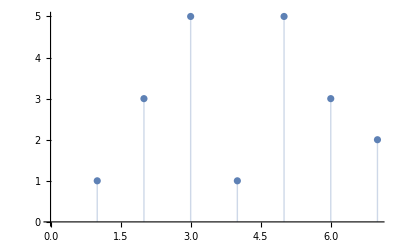

```mathematica
a={{1,1},{2,3},{3,5},{4,1},{5,5},{6,3},{7,2}}
ListPlot[a, Filling->Axis]
```

```mathematica
Times[2,3]
```

6

```mathematica
GetMean = Total[Map[(Times @@ #&),#]]/ Total[#[[All,2]]]&
```

Total[(Times@@#1&)/@#1]/Total[#1⟦All,2⟧]&

```mathematica
Map[(Times @@ #)&, a]
```

{1,6,15,4,25,18,14}

```mathematica
Total[Map[(Times @@ #)&, a]]
```

83

```mathematica
Total[a[[All,2]]]
```

20

```mathematica
GetMean[a]
```

83/20

```mathematica
N[GetMean @ a]
```

4.15

```mathematica
means = GetMean/@ Map[GetDistribution, data]
```

{6/5,12570715/11673293,1476/1369,1412/1305,938/885,148/147,149/139,95/92,373/309,224/215,825/706,226/167,462/145,115/107,251/109,145/137,727/682,3588/1213}

```mathematica
N /@ means
```

{1.2,1.07688,1.07816,1.08199,1.05989,1.0068,1.07194,1.03261,1.20712,1.04186,1.16856,1.35329,3.18621,1.07477,2.30275,1.05839,1.06598,2.95796}

```mathematica
namedMeans = Table[
{Map[GetLabel,data][[i]],N @means[[i]]},
{i, Length[means]}
] // TableForm
```

Gene:AKT1(ENSG00000142208) | 1.2
Gene:All | 1.07688
Gene:ATM(ENSG00000149311) | 1.07816
Gene:ATR(ENSG00000175054) | 1.08199
Gene:BRCA1(ENSG00000012048) | 1.05989
Gene:CDK2(ENSG00000123374) | 1.0068
Gene:CDKN1A(ENSG00000124762) | 1.07194
Gene:CHEK1(ENSG00000149554) | 1.03261
Gene:CHEK2(ENSG00000183765) | 1.20712
Gene:E2F1(ENSG00000101412) | 1.04186
Gene:ERBB2(ENSG00000141736) | 1.16856
Gene:HRAS(ENSG00000174775) | 1.35329
Gene:KRAS(ENSG00000133703) | 3.18621
Gene:MDM2(ENSG00000135679) | 1.07477
Gene:NRAS(ENSG00000213281) | 2.30275
Gene:RAF1(ENSG00000132155) | 1.05839
Gene:RB1(ENSG00000139687) | 1.06598
Gene:TP53(ENSG00000141510) | 2.95796

## Data display

```mathematica
labels = GetAxesLabels[data]
```

{MUTATIONS,AFFECTED_DONORS_PER_MUTATION}

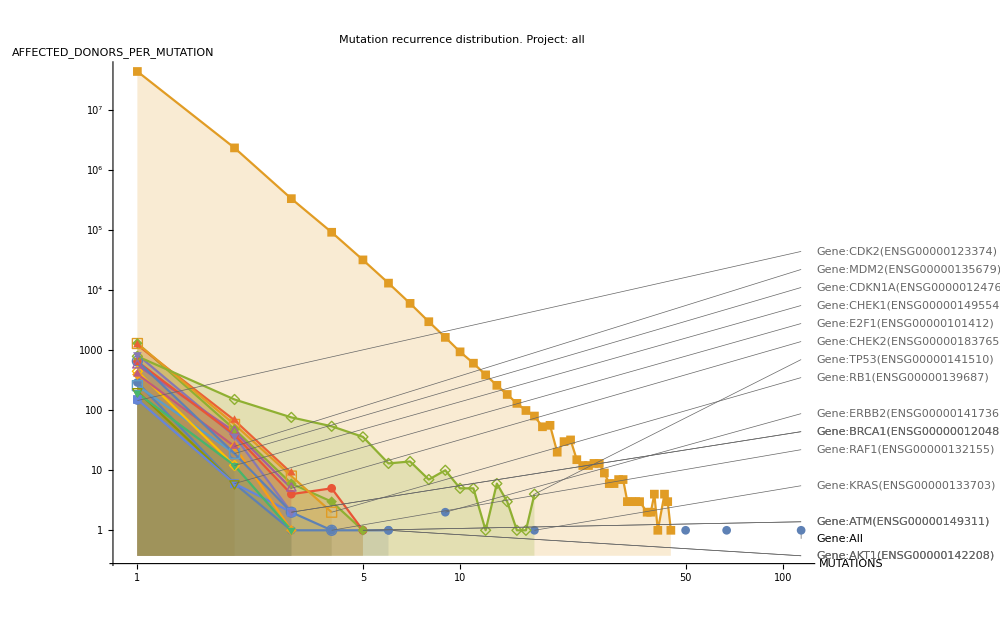

./logLogAllPlotsLabeled.png

```mathematica
logLogAllPlotsLabeled = Show[
ListLogLogPlot[#, 
Joined -> True, 
PlotMarkers-> Automatic, 
Filling->Bottom, 
ImageSize->1000,
AxesLabel->labels
]& [labeledDistributions],
PlotLabel->"Mutation recurrence distribution. Project: "<>project
]
Export[filename["logLogAllPlotsLabeled.png"], logLogAllPlotsLabeled]
```

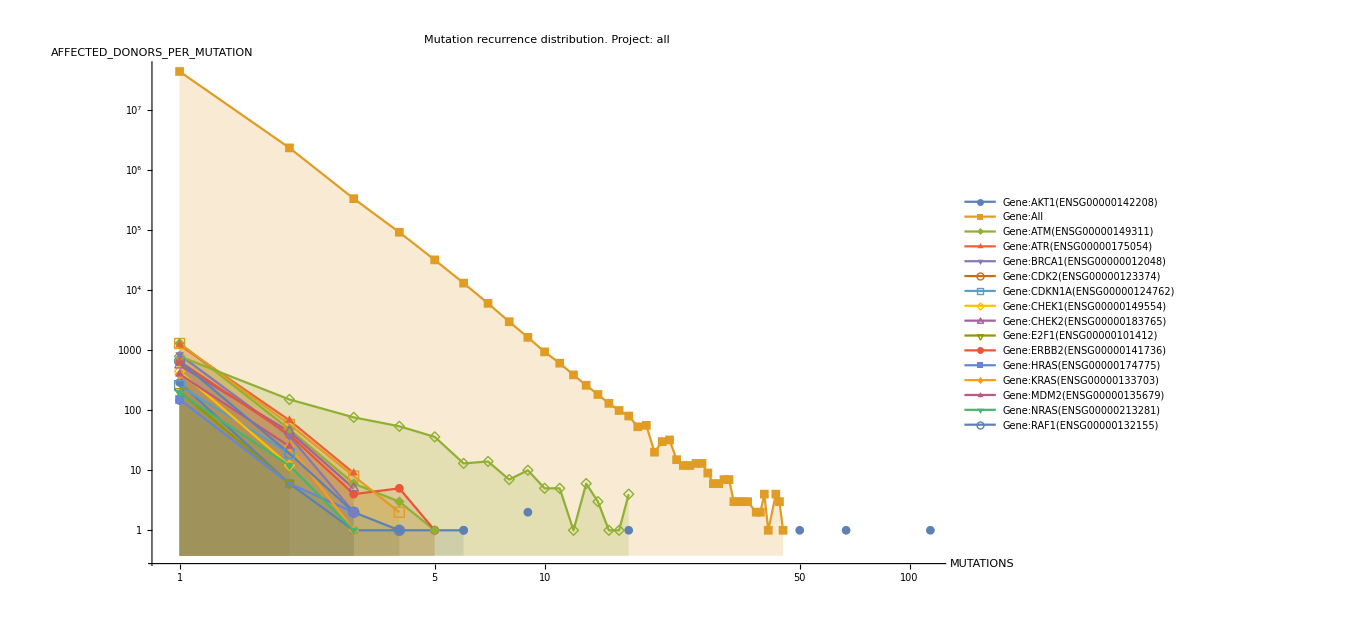

./logLogAllPlotsLegended.png

```mathematica
logLogAllPlotsLegended = Show[
ListLogLogPlot[#, 
Joined -> True, 
PlotMarkers-> Automatic, 
Filling->Bottom, 
ImageSize->1000,
AxesLabel->labels
]& [legendedDistributions],
PlotLabel->"Mutation recurrence distribution. Project: "<>project
]
Export[filename["logLogAllPlotsLegended.png"], logLogAllPlotsLegended]
```

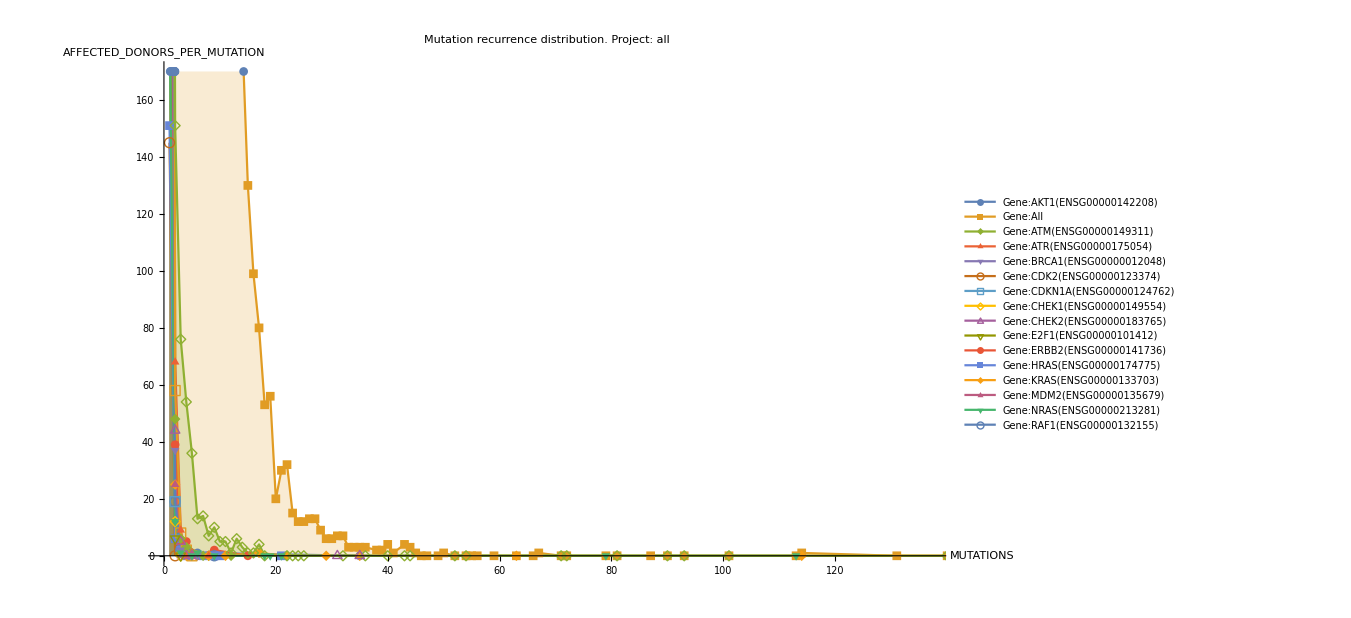

```mathematica
allPlotsLegended = Show[
ListPlot[#, 
Joined -> True, 
PlotMarkers-> Automatic, 
Filling->Bottom, 
ImageSize->1000,
AxesLabel->labels
]& [legendedDistributions],
PlotLabel->"Mutation recurrence distribution. Project: "<>project
]
```

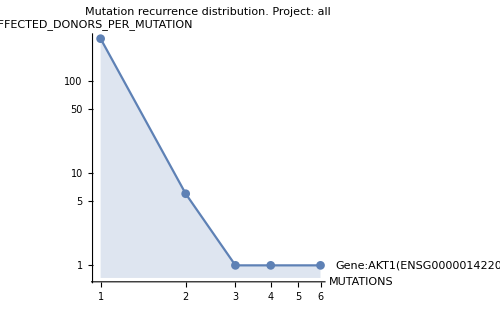
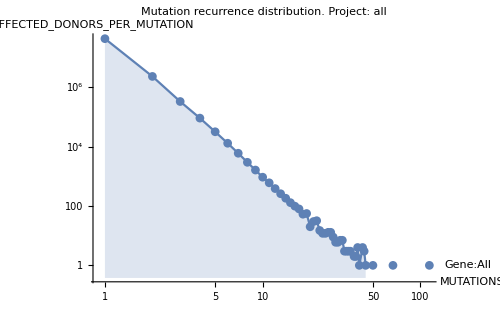
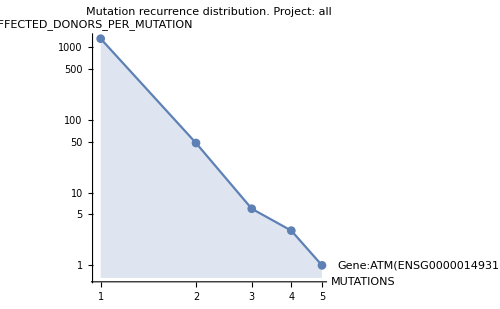
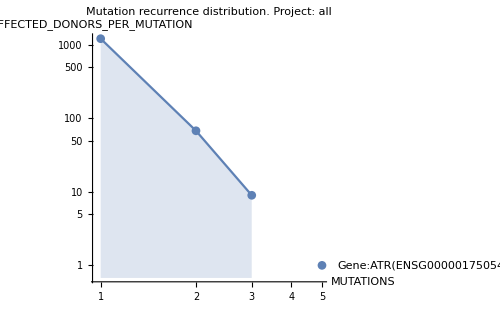
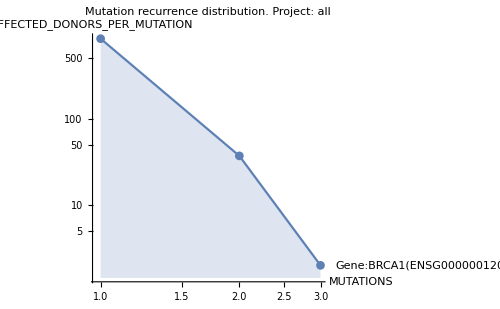
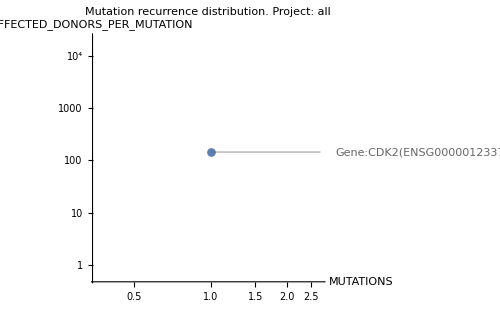
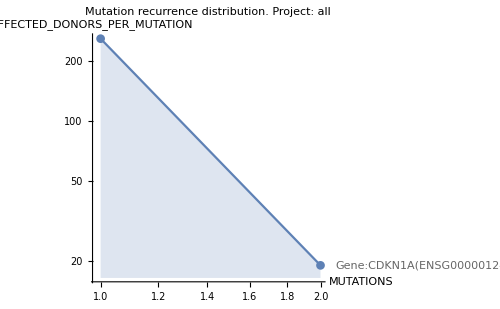
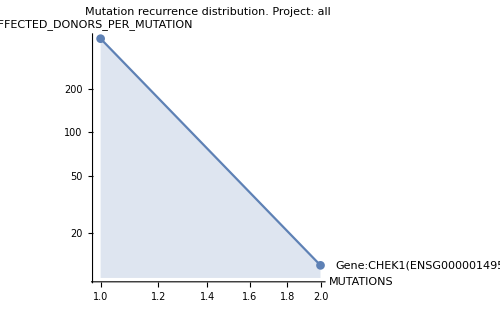

./logLogPlotGrid.png

```mathematica
LogLogPlots = Show[
ListLogLogPlot[#, 
Joined -> True, 
PlotMarkers-> Automatic, 
Filling->Bottom, 
ImageSize->500,
AxesLabel->labels
],
PlotLabel->"Mutation recurrence distribution. Project: "<>project
]& /@ labeledDistributions
LogLogPlotGrid = GraphicsGrid[Partition[LogLogPlots, UpTo[3]]];
Remove[LogLogPlots];
Export[filename["logLogPlotGrid.png"], LogLogPlotGrid]
Remove[LogLogPlotGrid];
```